So, we can start here by writing out the given values of Resistance and Capacitance which is (x10^3) and (x10^-6) for kilo and micro respectively. If we multiply these together we can get the time constant which we will use in out Charge and current expressions in place of RC. Then all we need to so is write out the functions and plot them.

110000

27/1000000

297/100

120

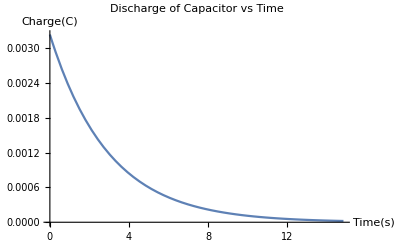

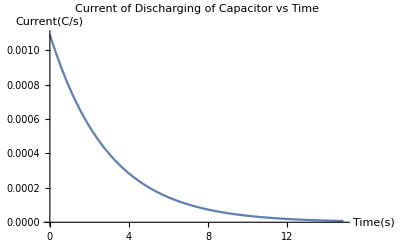

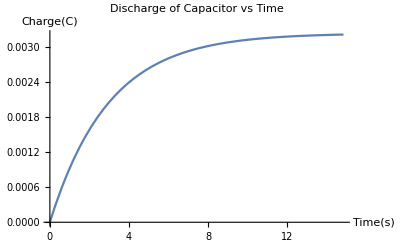

-Graphics-

```mathematica
(*Constants for Resistance, Capacitance, and time*)
R = 110*10^3
c = 27*10^(-6)
tcon = R*c
V0 = 120

(*Equations for Charge and Current from part a*)
Charge[t_]:=V0*c*Exp[-t/tcon]
Current[t_] :=(V0/R)*Exp[-t/tcon]

(*Plotting  of Charge and Current for part a*)
Plot[Charge[t],{t,0,5*tcon},AxesLabel->{"Time(s)","Charge(C)"},PlotLabel->"Discharge of Capacitor vs Time"]
Plot[Current[t],{t,0,5*tcon},AxesLabel->{"Time(s)","Current(C/s)"},PlotLabel->"Current of Discharging of Capacitor vs Time"]

(*Equations for Charge and Current from part c*)
Charge2[t_] :=V0*c*(1-Exp[-t/tcon])
Current2[t_] :=(V0/R)*Exp[-t/tcon]

(*Plotting  of Charge and Current for part c*)
Plot[Charge2[t],{t,0,5*tcon},AxesLabel->{"Time(s)","Charge(C)"},PlotLabel->"Discharge of Capacitor vs Time"]
Plot[Current2[t],{t,0,5*tcon},AxesLabel->{"Time(s)","Current(C/s)"},PlotLabel->"Current of Discharging of Capacitor vs Time"]
```